```mathematica
(*SetDirectory["D:\\study\\西安理工大学\\thesis\\论文\\标定后的数据"];
SetDirectory["D:\\study\\西安理工大学\\thesis\\论文\\codes\\data"];*)
```

```mathematica
Clear["@"];
```

Clear::wrsym: Symbol a is Protected.

Clear::wrsym: Symbol b is Protected.

Clear::wrsym: Symbol c is Protected.

General::stop: Further output of Clear will be suppressed during this calculation.

```mathematica
Needs["PlotLegends`"]
<<Data`;
(*For[i=51,i≤81,i++,
filen=FileNameJoin[{"E:\\work\\thesis\\kaiTi\\标定后的数据\\",StringJoin[{"calib_",ToString[i],".dat"}]}];
dd=Import[filen,"Data"];
d=Length[dd[[1]]];
If[Not EvenQ[d],Continue[];];
d=d/2;
pr=Table[BISLSfit[dd[[All,{2 j-1,2 j}]]],{j,d}];
Export["ca_"<>ToString[i]<>".txt",pr,"Table"];
]*)
```

```mathematica
(*dd=Reap[
Sow[Import["ca_"<>ToString[50]<>".txt","Data"]];
Sow[Import["ca_"<>ToString[52]<>".txt","Data"]];

];*)
```

```mathematica
(*dd=Table[Import["calib_"<>ToString[i]<>".dat","Data"],{i,51,53}];*)
(*dd=Table[Import["cc_"<>ToString[i+49]<>".mat","MAT"],{i,5,7}];*)
dd=ccData[3];
```

```mathematica
(*getList[x_]:=Flatten[Transpose[Partition[x,{1,2}]],2];
getListc[x_]:=Flatten[Transpose[Partition[x,{1,1}]],3];*)
```

```mathematica
Dimensions[dd[[3]]]
```

{8,32}

```mathematica
dp=Flatten[Transpose[Partition[dd[[1]],{1,2}]],2];
dp[[1]];
Dimensions[dp]
```

{128,2}

```mathematica
dp=Table[getListc[dd[[i]]],{i,3}];
Dimensions[dp]

dp[[1]]
```

{3,256}

{93.1721+9.64484 ⅈ,93.3244+9.23277 ⅈ,93.2901+8.96638 ⅈ,94.0644+8.95797 ⅈ,90.9324+8.93202 ⅈ,90.8784+9.07087 ⅈ,91.0633+8.92884 ⅈ,93.8181+9.1163 ⅈ,90.5972+10.1141 ⅈ,90.8334+9.97996 ⅈ,90.8904+9.82571 ⅈ,91.4407+9.85291 ⅈ,88.3878+9.80495 ⅈ,88.4361+9.73219 ⅈ,88.6965+9.65118 ⅈ,90.3532+9.86337 ⅈ,89.0616+10.683 ⅈ,89.3309+10.6204 ⅈ,89.4078+10.5663 ⅈ,89.993+10.5558 ⅈ,86.9305+10.3966 ⅈ,87.065+10.3665 ⅈ,87.3124+10.3186 ⅈ,88.6612+10.4937 ⅈ,87.9889+11.2092 ⅈ,88.2367+11.1625 ⅈ,88.3616+11.1313 ⅈ,88.9291+11.1871 ⅈ,85.876+10.94 ⅈ,86.0244+10.8827 ⅈ,86.2941+10.9015 ⅈ,87.3896+11.0864 ⅈ,87.1474+11.7054 ⅈ,87.32+11.6975 ⅈ,87.4173+11.6484 ⅈ,87.9191+11.6684 ⅈ,84.9551+11.426 ⅈ,85.0879+11.4136 ⅈ,85.3337+11.386 ⅈ,86.3029+11.6073 ⅈ,86.2749+12.248 ⅈ,86.5126+12.2818 ⅈ,86.6434+12.2849 ⅈ,87.0933+12.3177 ⅈ,84.2489+12.0054 ⅈ,84.2786+12.0096 ⅈ,84.5225+11.9992 ⅈ,85.3909+12.2138 ⅈ,85.4215+12.6292 ⅈ,85.538+12.6617 ⅈ,85.6171+12.6734 ⅈ,86.1436+12.7359 ⅈ,83.2804+12.3423 ⅈ,83.4012+12.3454 ⅈ,83.5673+12.3849 ⅈ,84.274+12.5948 ⅈ,84.7687+13.0017 ⅈ,84.9421+13.0587 ⅈ,85.0379+13.0278 ⅈ,85.4629+13.0929 ⅈ,82.6688+12.7092 ⅈ,82.7303+12.7038 ⅈ,82.9312+12.7791 ⅈ,83.5623+12.9511 ⅈ,84.1544+13.1782 ⅈ,84.355+13.2549 ⅈ,84.434+13.2673 ⅈ,84.8634+13.3044 ⅈ,81.9742+12.8808 ⅈ,82.0882+12.9281 ⅈ,82.0215+13.0937 ⅈ,82.8944+13.144 ⅈ,83.451+13.3368 ⅈ,83.6514+13.4138 ⅈ,83.7303+13.4264 ⅈ,84.1893+13.4699 ⅈ,81.3242+13.0843 ⅈ,81.4252+13.0859 ⅈ,81.2745+13.2655 ⅈ,82.1791+13.3101 ⅈ,78.6001+13.1955 ⅈ,78.6622+13.2482 ⅈ,78.7434+13.2478 ⅈ,79.1547+13.2744 ⅈ,76.4208+13.0079 ⅈ,76.5429+12.9463 ⅈ,76.2896+13.1227 ⅈ,77.2489+13.1489 ⅈ,74.4845+14.0067 ⅈ,74.4771+14.0457 ⅈ,74.5705+14.0363 ⅈ,75.0029+14.0635 ⅈ,72.3308+13.824 ⅈ,72.4804+13.787 ⅈ,72.0903+13.8041 ⅈ,73.0601+13.9502 ⅈ,71.3178+14.1601 ⅈ,71.3325+14.1889 ⅈ,71.384+14.1862 ⅈ,71.8353+14.2238 ⅈ,69.2023+13.9788 ⅈ,69.3419+13.944 ⅈ,69.1286+13.8886 ⅈ,69.859+14.0607 ⅈ,68.8936+13.9915 ⅈ,68.9279+14.0235 ⅈ,68.9524+14.0035 ⅈ,69.3861+14.0285 ⅈ,66.8098+13.7992 ⅈ,66.91+13.759 ⅈ,66.7506+13.6898 ⅈ,67.4291+13.8657 ⅈ,67.0735+13.6584 ⅈ,67.0711+13.6701 ⅈ,67.1174+13.643 ⅈ,67.546+13.6933 ⅈ,64.9859+13.4343 ⅈ,65.1128+13.4131 ⅈ,64.9603+13.3108 ⅈ,65.5606+13.4696 ⅈ,65.4105+13.3555 ⅈ,65.3909+13.3515 ⅈ,65.4664+13.3312 ⅈ,65.8948+13.3825 ⅈ,63.4115+13.0973 ⅈ,63.4749+13.0873 ⅈ,63.3318+12.9886 ⅈ,63.915+13.1315 ⅈ,64.066+12.9412 ⅈ,64.0638+12.9524 ⅈ,64.1565+12.9479 ⅈ,64.5207+12.9628 ⅈ,62.1086+12.6813 ⅈ,62.1598+12.6805 ⅈ,62.0718+12.561 ⅈ,62.5967+12.6899 ⅈ,63.0045+12.5895 ⅈ,63.0023+12.6005 ⅈ,63.0557+12.5883 ⅈ,63.4862+12.6282 ⅈ,61.0491+12.3208 ⅈ,61.0982+12.3306 ⅈ,60.9998+12.2111 ⅈ,61.5446+12.3425 ⅈ,62.0134+12.189 ⅈ,62.0604+12.2095 ⅈ,62.0646+12.1878 ⅈ,62.481+12.247 ⅈ,60.1207+11.9151 ⅈ,60.1774+11.9373 ⅈ,60.1001+11.813 ⅈ,60.5963+11.9325 ⅈ,60.4849+11.6147 ⅈ,60.487+11.6042 ⅈ,60.5479+11.6049 ⅈ,60.9194+11.632 ⅈ,58.6249+11.3318 ⅈ,58.6975+11.3246 ⅈ,58.6386+11.2071 ⅈ,59.1062+11.3179 ⅈ,59.2881+10.9456 ⅈ,59.2802+10.9334 ⅈ,59.402+10.9345 ⅈ,59.7304+10.9734 ⅈ,57.4436+10.6362 ⅈ,57.5124+10.6489 ⅈ,57.4799+10.5495 ⅈ,57.9169+10.6611 ⅈ,58.2717+10.4427 ⅈ,58.3012+10.448 ⅈ,58.3657+10.4281 ⅈ,58.73+10.4931 ⅈ,56.5044+10.1566 ⅈ,56.5635+10.1672 ⅈ,56.5534+10.0533 ⅈ,56.9419+10.1531 ⅈ,57.4736+9.95841 ⅈ,57.4736+9.95841 ⅈ,57.5478+9.94023 ⅈ,57.8945+9.9897 ⅈ,55.7378+9.66767 ⅈ,55.7871+9.67621 ⅈ,55.7743+9.57375 ⅈ,56.1536+9.66914 ⅈ,56.7871+9.46215 ⅈ,56.7969+9.46379 ⅈ,56.8907+9.4488 ⅈ,57.2179+9.49288 ⅈ,55.0707+9.17616 ⅈ,55.1299+9.18602 ⅈ,55.1672+9.08342 ⅈ,55.5358+9.18393 ⅈ,54.6612+7.90602 ⅈ,54.6881+7.9294 ⅈ,54.7588+7.92989 ⅈ,55.0868+7.96757 ⅈ,53.0282+7.66982 ⅈ,53.1033+7.70908 ⅈ,53.1451+7.62992 ⅈ,53.4875+7.70767 ⅈ,53.6273+6.74618 ⅈ,53.6349+6.76615 ⅈ,53.7365+6.75991 ⅈ,54.0639+6.8011 ⅈ,52.0521+6.52956 ⅈ,52.128+6.56681 ⅈ,52.1536+6.5238 ⅈ,52.4974+6.59473 ⅈ,52.9854+6.14 ⅈ,52.9999+6.18855 ⅈ,53.0848+6.15151 ⅈ,53.3927+6.18719 ⅈ,51.3992+5.92891 ⅈ,51.4823+5.99314 ⅈ,51.5174+5.95165 ⅈ,51.8499+6.03592 ⅈ,52.5856+5.6662 ⅈ,52.5687+5.72936 ⅈ,52.6562+5.66451 ⅈ,52.9336+5.70369 ⅈ,50.9797+5.44816 ⅈ,51.0705+5.53901 ⅈ,51.1151+5.49872 ⅈ,51.4265+5.59578 ⅈ,52.327+5.35209 ⅈ,52.3337+5.48202 ⅈ,52.4128+5.39784 ⅈ,52.6406+5.43059 ⅈ,50.767+5.17462 ⅈ,50.8545+5.30016 ⅈ,50.8754+5.29336 ⅈ,51.1393+5.36593 ⅈ,52.1436+5.17705 ⅈ,52.1607+5.30749 ⅈ,52.2603+5.21627 ⅈ,52.4466+5.26261 ⅈ,50.5757+4.97682 ⅈ,50.6602+5.13694 ⅈ,50.6955+5.18522 ⅈ,50.9623+5.23048 ⅈ,52.0477+5.23175 ⅈ,52.0907+5.40143 ⅈ,52.2076+5.33988 ⅈ,52.3948+5.37751 ⅈ,50.4926+5.00423 ⅈ,50.5969+5.26438 ⅈ,50.6491+5.34131 ⅈ,50.9129+5.41406 ⅈ,51.8505+5.19365 ⅈ,51.8255+5.43793 ⅈ,51.9107+5.39192 ⅈ,51.8709+5.38779 ⅈ,50.2663+4.95523 ⅈ,50.2893+5.32111 ⅈ,50.233+5.37723 ⅈ,50.3249+5.45814 ⅈ}

```mathematica
aa=Transpose[{Re[Flatten[dp[[2,All]]]],Im[Flatten[dp[[2,All]]]]}];
Dimensions[aa]
bb=Transpose[{Re[Flatten[dp[[1,All]]]],Im[Flatten[dp[[1,All]]]]}];
```

{256,2}

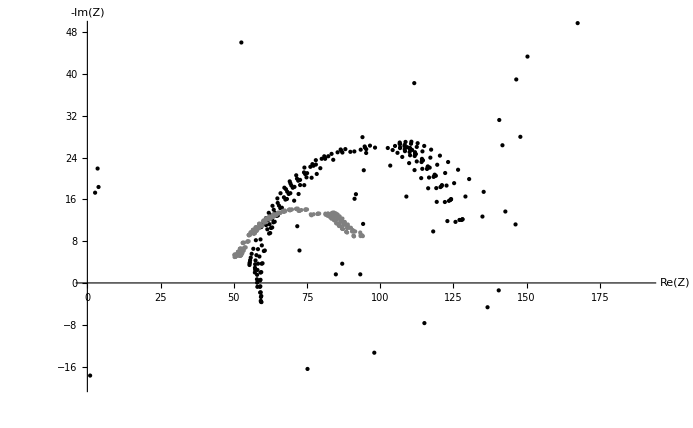

```mathematica
ListPlot[{aa,bb},AxesLabel->{"Re(Z)","-Im(Z)"},PlotStyle->{Black,Gray},MeshStyle->PointSize[0.3](*,PlotLegend->{"第一人测量数据","第二人测量数据"},LegendShadow->None*)]
```

```mathematica
f1=dp[[1]];
f2=dp[[2]];
```

```mathematica
p1=Partition[f1,32]
```

{{{85.61,-1.19},{85.02,-2.87},{84.51,-4.76},{84.04,-5.99},{83.47,-6.68},{83.01,-7.41},{82.31,-7.87},{81.81,-8.41},{81.34,-8.79},{80.67,-9.16},{75.67,-10.88},{71.2,-12.78},{67.55,-13.78},{64.63,-14.21},{62.34,-14.31},{60.32,-14.36},{58.58,-14.18},{57.2,-13.93},{56.03,-13.6},{54.18,-13.08},{52.7,-12.41},{51.51,-11.83},{50.56,-11.22},{49.76,-10.5},{47.49,-8.13},{46.46,-6.17},{45.85,-4.88},{45.57,-3.12},{45.53,-1.23},{45.42,-1.49},{45.54,-0.81},{45.66,0.16}},{{86.03,-4.98},{85.39,-2.93},{84.86,-4.66},{84.3,-5.99},{83.78,-6.7},{83.27,-7.42},{82.56,-7.97},{82.12,-8.47},{81.59,-8.86},{80.99,-9.22},{75.9,-10.93},{71.41,-12.86},{67.76,-13.86},{64.82,-14.32},{62.55,-14.41},{60.48,-14.47},{58.79,-14.29},{57.41,-14.06},{56.21,-13.72},{54.37,-13.19},{52.89,-12.52},{51.68,-11.95},{50.72,-11.35},{49.92,-10.68},{47.58,-8.41},{46.54,-6.52},{45.88,-5.28},{45.49,-4.15},{45.31,-3.26},{45.25,-2.43},{45.39,-1.9},{45.16,-1.31}},{{93.35,-0.38},{90.83,-2.71},{89.33,-4.56},{88.22,-5.96},{87.2,-6.69},{86.27,-7.41},{85.19,-8.01},{84.45,-8.51},{83.68,-8.92},{82.83,-9.28},{77.46,-10.97},{72.68,-12.87},{68.81,-13.88},{65.67,-14.36},{63.17,-14.46},{61.01,-14.49},{59.11,-14.31},{57.65,-14.02},{56.41,-13.73},{54.54,-13.2},{53.03,-12.54},{51.82,-11.98},{50.84,-11.38},{50.01,-10.71},{47.68,-8.44},{46.61,-6.57},{45.96,-5.33},{45.57,-4.23},{45.39,-3.36},{45.31,-2.53},{45.46,-2.01},{45.14,-1.44}},{{94.88,-0.12},{92.04,-2.64},{90.34,-4.56},{89.,-5.94},{87.78,-6.68},{86.76,-7.42},{85.5,-8.},{84.62,-8.5},{83.7,-8.92},{82.75,-9.3},{77.31,-10.99},{72.47,-12.87},{68.56,-13.89},{65.37,-14.37},{62.81,-14.46},{60.62,-14.53},{58.69,-14.36},{57.21,-14.12},{55.79,-13.83},{53.82,-13.34},{52.27,-12.73},{51.,-12.22},{49.96,-11.65},{49.09,-11.07},{46.78,-9.04},{45.69,-7.46},{45.04,-6.54},{44.64,-5.81},{44.42,-5.37},{44.34,-5.09},{44.53,-5.14},{44.14,-5.36}},{{85.59,-1.01},{84.96,-2.86},{84.47,-4.68},{83.96,-6.},{83.38,-6.68},{82.83,-7.41},{82.07,-7.93},{81.64,-8.43},{81.15,-8.82},{80.5,-9.15},{75.49,-10.78},{71.05,-12.61},{67.51,-13.56},{64.66,-14.},{62.44,-14.08},{60.47,-14.11},{58.8,-13.94},{57.42,-13.71},{56.29,-13.41},{54.5,-12.9},{53.03,-12.26},{51.87,-11.72},{50.88,-11.15},{50.12,-10.5},{47.82,-8.34},{46.75,-6.5},{46.09,-5.3},{45.71,-4.21},{45.55,-3.35},{45.45,-2.53},{45.53,-1.94},{45.49,-1.23}},{{85.66,-5.08},{85.11,-2.86},{84.6,-4.57},{84.08,-5.96},{83.49,-6.67},{82.96,-7.4},{82.22,-7.93},{81.76,-8.46},{81.23,-8.79},{80.61,-9.16},{75.55,-10.77},{71.13,-12.6},{67.57,-13.57},{64.74,-14.},{62.49,-14.08},{60.53,-14.13},{58.87,-13.95},{57.52,-13.7},{56.37,-13.4},{54.58,-12.9},{53.11,-12.26},{51.93,-11.73},{50.99,-11.16},{50.18,-10.52},{47.89,-8.4},{46.82,-6.58},{46.14,-5.39},{45.76,-4.32},{45.61,-3.46},{45.54,-2.67},{45.65,-2.14},{45.51,-1.55}},{{85.83,-5.08},{85.28,-2.91},{84.8,-4.56},{84.28,-5.96},{83.7,-6.66},{83.18,-7.41},{82.42,-7.93},{81.93,-8.44},{81.4,-8.82},{80.79,-9.15},{75.73,-10.8},{71.32,-12.6},{67.73,-13.57},{64.87,-14.01},{62.64,-14.1},{60.66,-14.12},{59.,-13.94},{57.66,-13.68},{56.51,-13.4},{54.71,-12.9},{53.27,-12.28},{52.09,-11.75},{51.13,-11.16},{50.33,-10.54},{48.05,-8.4},{46.96,-6.59},{46.29,-5.43},{45.9,-4.35},{45.71,-3.51},{45.62,-2.74},{45.74,-2.25},{45.5,-1.68}},{{90.86,-1.33},{88.89,-2.68},{87.79,-4.58},{86.82,-5.96},{85.93,-6.73},{85.13,-7.5},{84.13,-8.08},{83.47,-8.58},{82.72,-8.96},{81.96,-9.33},{76.6,-10.96},{71.88,-12.76},{68.11,-13.7},{65.07,-14.09},{62.67,-14.15},{60.65,-14.15},{58.98,-13.95},{57.61,-13.67},{56.47,-13.36},{54.67,-12.85},{53.21,-12.2},{52.05,-11.66},{51.08,-11.05},{50.31,-10.44},{48.04,-8.3},{46.97,-6.53},{46.29,-5.37},{45.88,-4.33},{45.66,-3.5},{45.58,-2.72},{45.73,-2.27},{45.35,-1.74}}}

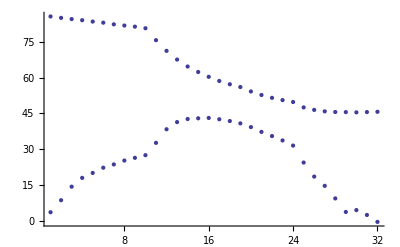

```mathematica
Show[ListPlot[dp[[Range[32],1]]],ListPlot[-3*dp[[Range[32],2]]]]
(*,Joined->True,PlotRange->{40,90}*)
```